# Circuit 1

## Module

```mathematica
(*Gates*)
Rx[θ_]:={{Cos[θ/2],-I Sin[θ/2]},{-I Sin[θ/2],Cos[θ/2]}}
Ry[θ_]:={{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}}
Rz[θ_]:={{Exp[-I θ/2],0},{0,Exp[I θ/2]}}
(*Tensor calculation*)
TwoQubit[mat1_,mat2_]:=TensorProduct[mat1,mat2]//ArrayFlatten
FourQubit[{mat1_,mat2_,mat3_,mat4_}]:=TensorProduct[TwoQubit[mat1,mat2],TwoQubit[mat3,mat4]]//ArrayFlatten
```

```mathematica
(*Parameter condition*)
condition={θ[1]∈Reals,θ[1]≥0,θ[2]∈Reals,θ[2]≥0,θ[3]∈Reals,θ[3]≥0,θ[4]∈Reals,θ[4]≥0,θ[5]∈Reals,θ[5]≥0,θ[6]∈Reals,θ[6]≥0,θ[7]∈Reals,θ[7]≥0,θ[8]∈Reals,θ[8]≥0,1≥x≥0,1≥y≥0,x∈Reals,y∈Reals}
```

{θ[1]∈ℝ,θ[1]≥0,θ[2]∈ℝ,θ[2]≥0,θ[3]∈ℝ,θ[3]≥0,θ[4]∈ℝ,θ[4]≥0,θ[5]∈ℝ,θ[5]≥0,θ[6]∈ℝ,θ[6]≥0,θ[7]∈ℝ,θ[7]≥0,θ[8]∈ℝ,θ[8]≥0,1≥x≥0,1≥y≥0,x∈ℝ,y∈ℝ}

```mathematica
(*input state |0000>*)
input=Flatten[FourQubit[{0,1},{0,1},{0,1},{0,1}]];
(*Embedding Circuit*)
Embeding=Assuming[condition,FourQubit[Table[Rz[Pi/4],{i,1,4}]].FourQubit[Table[Ry[Pi/4],{i,1,4}]].FourQubit[Rx[x],Rx[y],Rx[x],Rx[y]]//Simplify];
(*Example Circuit 1*)
circuit1=Assuming[condition,FourQubit[Table[Rz[θ[i+4]],{i,1,4}]].FourQubit[Table[Rx[θ[i]],{i,1,4}]]];
```

```mathematica
(*result state*)
result=circuit1.Embeding.input;
(*Print First element*)
%[[1]]/.{x->0,y->0} //Simplify
```

1/8 ⅇ^(-1/2 ⅈ (θ[5]+θ[6]+θ[7]+θ[8])) (Sin[θ[1]/2] (-Sin[θ[2]/2] (Cos[θ[3]/2]-(2-2 ⅈ) Cos[π/8]^2 Sin[θ[3]/2]) (Cos[θ[4]/2]-(2-2 ⅈ) Cos[π/8]^2 Sin[θ[4]/2])+Cos[θ[2]/2] (Cos[θ[3]/2] ((2+2 ⅈ) Cos[θ[4]/2] Sin[π/8]^2-Sin[θ[4]/2])-Sin[θ[3]/2] (Cos[θ[4]/2]-(2-2 ⅈ) Cos[π/8]^2 Sin[θ[4]/2])))+Cos[θ[1]/2] (-Cos[θ[2]/2] ((2+2 ⅈ) Cos[θ[3]/2] Sin[π/8]^2-Sin[θ[3]/2]) ((2+2 ⅈ) Cos[θ[4]/2] Sin[π/8]^2-Sin[θ[4]/2])+Sin[θ[2]/2] (Cos[θ[3]/2] ((2+2 ⅈ) Cos[θ[4]/2] Sin[π/8]^2-Sin[θ[4]/2])-Sin[θ[3]/2] (Cos[θ[4]/2]-(2-2 ⅈ) Cos[π/8]^2 Sin[θ[4]/2]))))

```mathematica
result
```

## Test

```mathematica
(*Test Norm is equal to 1*)
Norm[result/.Table[θ[i]->1,{i,1,8}]/.{x->1,y->1}//N]
```

1.

```mathematica
(*Probability amplitute for each base*)
ProbAmp1=Table[Norm[(result[[j]]/.Table[θ[i]->0,{i,1,8}]/.{x->1,y->1})//N],{j,1,16}];
(*Sum of Prob square eqaul to 1*)
Total[ProbAmp1^2]
```

1.

```mathematica
fun[x1_,y1_,param1_]:=Module[{param,data,loc,conv,max,ProbAmp},
param=Table[θ[i]->param1[[i]],{i,1,8}];
data={x->x1,y->y1};
ProbAmp=Table[Norm[(result[[j]]/.param/.data)],{j,1,16}];
max=Max[ProbAmp];
loc=Position[ProbAmp,max][[1,1]];
conv=If[MemberQ[{1,2,3,4,13,14,15,16},loc],0,1];
conv
]
```

```mathematica
Clear[dataStorage]
dataStorage[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_]:=dataStorage[x1,x2,x3,x4,x5,x6,x7,x8]=Table[fun[x,y,{x1,x2,x3,x4,x5,x6,x7,x8}],{x,0,1,0.25},{y,0,1,0.25}]
```

```mathematica
(*We cannot optimize all the paramter because it will take 52 hours, so Take one parameter out 13 hours*)
Monitor[
Do[dataStorage[x1,x2,x3,x4,x5,x6,x7,0],{x1,0,2Pi-0.1,Pi/2},{x2,0,2Pi-0.1,Pi/2},{x3,0,2Pi-0.1,Pi/2},{x4,0,2Pi-0.1,Pi/2},{x5,0,2Pi-0.1,Pi/2},{x6,0,2Pi-0.1,Pi/2},{x7,0,2Pi-0.1,Pi/2}]
,{x1,x2,x3,x4,x5,x6,x7,0}]
```

```mathematica
data=Table[dataStorage[x1,x2,x3,x4,x5,x6,x7,0],{x1,0,2Pi-0.1,Pi/2},{x2,0,2Pi-0.1,Pi/2},{x3,0,2Pi-0.1,Pi/2},{x4,0,2Pi-0.1,Pi/2},{x5,0,2Pi-0.1,Pi/2},{x6,0,2Pi-0.1,Pi/2},{x7,0,2Pi-0.1,Pi/2}];
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\GitHub\\Quantum_Machine_Learning_Express\\Analytical"]
Export["PQC_analytical_circuit1.csv",data]
```

C:\Users\Saesun Kim\Documents\GitHub\Quantum_Machine_Learning_Express\Analytical

PQC_analytical_circuit1.csv

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\GitHub\\Quantum_Machine_Learning_Express\\Analytical"]
data=Import["PQC_analytical_circuit1.csv","Table"]
```

C:\Users\Saesun Kim\Documents\GitHub\Quantum_Machine_Learning_Express\Analytical

$Aborted

```mathematica
data[[1,1,1]]
```

Part::partd: Part specification {«1»}⟦1,1,1⟧ is longer than depth of object.

{1}⟦1,1,1⟧
 |  |  |  |

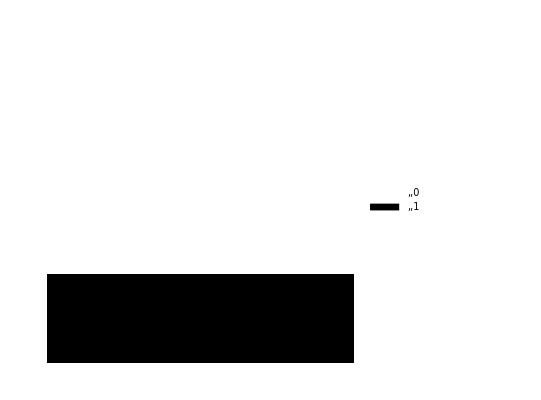

```mathematica
Do[
param1={3.14+0.4,3*3.14/2-0.3,0,0,0,0,0,0};
param=Table[θ[i]->param1[[i]],{i,1,8}];
data1={x->1x1,y->1x1};
ProbAmp=Table[Norm[(result[[j]]/.param/.data1)],{j,1,16}];
max=Max[ProbAmp];
loc=Position[ProbAmp,max][[1,1]];
conv[x1,y1]=If[MemberQ[{1,2,3,4,13,14,15,16},loc],0,1];
,{x1,0,1,0.1},{y1,0,1,0.1}]
ArrayPlot[Table[conv[x1,y1],{x1,0,1,0.1},{y1,0,1,0.1}],PlotLegends->Automatic]
```

```mathematica
Do[
param1={1,2,0,0,0,0,0,0};
param=Table[θ[i]->param1[[i]],{i,1,8}];
data1={x->10x1,y->10x1};
ProbAmp=Table[Norm[(result[[j]]/.param/.data1)],{j,1,16}];
max=Max[ProbAmp];
loc=Position[ProbAmp,max][[1,1]];
conv[x1,y1]=If[MemberQ[{1,2,3,4,13,14,15,16},loc],0,1];
,{x1,0,1,0.05},{y1,0,1,0.05}]
ArrayPlot[Table[conv[x1,y1],{x1,0,1,0.05},{y1,0,1,0.05}],PlotLegends->Automatic]
```

-Graphics-

```mathematica
circuit1
```

{{ⅇ^(-1/2 ⅈ (θ[5]+θ[6]+θ[7]+θ[8])) Cos[θ[1]/2] Cos[θ[2]/2] Cos[θ[3]/2] Cos[θ[4]/2],-ⅈ ⅇ^(-1/2 ⅈ (θ[5]+θ[6]+θ[7]+θ[8])) Cos[θ[1]/2] Cos[θ[2]/2] Cos[θ[3]/2] Sin[θ[4]/2],-ⅈ ⅇ^(-1/2 ⅈ (θ[5]+θ[6]+θ[7]+θ[8])) Cos[θ[1]/2] Cos[θ[2]/2] Cos[θ[4]/2] Sin[θ[3]/2],-ⅇ^(-1/2 ⅈ (θ[5]+θ[6]+θ[7]+θ[8])) Cos[θ[1]/2] Cos[θ[2]/2] Sin[θ[3]/2] Sin[θ[4]/2],-ⅈ ⅇ^(-1/2 ⅈ (θ[5]+θ[6]+θ[7]+θ[8])) Cos[θ[1]/2] Cos[θ[3]/2] Cos[θ[4]/2] Sin[θ[2]/2],-ⅇ^(-1/2 ⅈ (θ[5]+θ[6]+θ[7]+θ[8])) Cos[θ[1]/2] Cos[θ[3]/2] Sin[θ[2]/2] Sin[θ[4]/2],5,ⅈ ⅇ^(-1/2 ⅈ (θ[5]+θ[6]+θ[7]+θ[8])) Cos[θ[2]/2] Sin[θ[1]/2] Sin[θ[3]/2] Sin[θ[4]/2],-ⅇ^(-1/2 ⅈ (θ[5]+θ[6]+θ[7]+θ[8])) Cos[θ[3]/2] Cos[θ[4]/2] Sin[θ[1]/2] Sin[θ[2]/2],ⅈ ⅇ^(-1/2 ⅈ (θ[5]+θ[6]+θ[7]+θ[8])) Cos[θ[3]/2] Sin[θ[1]/2] Sin[θ[2]/2] Sin[θ[4]/2],ⅈ ⅇ^(-1/2 ⅈ (θ[5]+θ[6]+θ[7]+θ[8])) Cos[θ[4]/2] Sin[θ[1]/2] Sin[θ[2]/2] Sin[θ[3]/2],ⅇ^(-1/2 ⅈ (θ[5]+θ[6]+θ[7]+θ[8])) Sin[θ[1]/2] Sin[θ[2]/2] Sin[θ[3]/2] Sin[θ[4]/2]},14,{ⅇ^(1/2 ⅈ (1)) Sin[θ[1]/2] Sin[θ[2]/2] Sin[θ[3]/2] Sin[θ[4]/2],14,1}}
 |  |  |  |

```mathematica
küçükçekmece
Join Zoom Meeting
https://us04web.zoom.us/j/78575754151?pwd=Tzh4cVloQ20zV0gxNk85WWx3SmN1QT09

Meeting ID:785 7575 4151
Passcode:05Ln4T
```

```mathematica
param1={1,2,1,2,0,0,0,0};
param=Table[θ[i]->param1[[i]],{i,1,8}];
Table[(circuit1[[j]]/.param),{j,1,16}]//N
```

{{0.224828,0.-0.350148 ⅈ,0.-0.122824 ⅈ,-0.191287,0.-0.350148 ⅈ,-0.545324,-0.191287,0.+0.297912 ⅈ,0.-0.122824 ⅈ,-0.191287,-0.067099,0.+0.1045 ⅈ,-0.191287,0.+0.297912 ⅈ,0.+0.1045 ⅈ,0.16275},{0.-0.350148 ⅈ,0.224828,-0.191287,0.-0.122824 ⅈ,-0.545324,0.-0.350148 ⅈ,0.+0.297912 ⅈ,-0.191287,-0.191287,0.-0.122824 ⅈ,0.+0.1045 ⅈ,-0.067099,0.+0.297912 ⅈ,-0.191287,0.16275,0.+0.1045 ⅈ},{0.-0.122824 ⅈ,-0.191287,0.224828,0.-0.350148 ⅈ,-0.191287,0.+0.297912 ⅈ,0.-0.350148 ⅈ,-0.545324,-0.067099,0.+0.1045 ⅈ,0.-0.122824 ⅈ,-0.191287,0.+0.1045 ⅈ,0.16275,-0.191287,0.+0.297912 ⅈ},{-0.191287,0.-0.122824 ⅈ,0.-0.350148 ⅈ,0.224828,0.+0.297912 ⅈ,-0.191287,-0.545324,0.-0.350148 ⅈ,0.+0.1045 ⅈ,-0.067099,-0.191287,0.-0.122824 ⅈ,0.16275,0.+0.1045 ⅈ,0.+0.297912 ⅈ,-0.191287},{0.-0.350148 ⅈ,-0.545324,-0.191287,0.+0.297912 ⅈ,0.224828,0.-0.350148 ⅈ,0.-0.122824 ⅈ,-0.191287,-0.191287,0.+0.297912 ⅈ,0.+0.1045 ⅈ,0.16275,0.-0.122824 ⅈ,-0.191287,-0.067099,0.+0.1045 ⅈ},{-0.545324,0.-0.350148 ⅈ,0.+0.297912 ⅈ,-0.191287,0.-0.350148 ⅈ,0.224828,-0.191287,0.-0.122824 ⅈ,0.+0.297912 ⅈ,-0.191287,0.16275,0.+0.1045 ⅈ,-0.191287,0.-0.122824 ⅈ,0.+0.1045 ⅈ,-0.067099},{-0.191287,0.+0.297912 ⅈ,0.-0.350148 ⅈ,-0.545324,0.-0.122824 ⅈ,-0.191287,0.224828,0.-0.350148 ⅈ,0.+0.1045 ⅈ,0.16275,-0.191287,0.+0.297912 ⅈ,-0.067099,0.+0.1045 ⅈ,0.-0.122824 ⅈ,-0.191287},{0.+0.297912 ⅈ,-0.191287,-0.545324,0.-0.350148 ⅈ,-0.191287,0.-0.122824 ⅈ,0.-0.350148 ⅈ,0.224828,0.16275,0.+0.1045 ⅈ,0.+0.297912 ⅈ,-0.191287,0.+0.1045 ⅈ,-0.067099,-0.191287,0.-0.122824 ⅈ},{0.-0.122824 ⅈ,-0.191287,-0.067099,0.+0.1045 ⅈ,-0.191287,0.+0.297912 ⅈ,0.+0.1045 ⅈ,0.16275,0.224828,0.-0.350148 ⅈ,0.-0.122824 ⅈ,-0.191287,0.-0.350148 ⅈ,-0.545324,-0.191287,0.+0.297912 ⅈ},{-0.191287,0.-0.122824 ⅈ,0.+0.1045 ⅈ,-0.067099,0.+0.297912 ⅈ,-0.191287,0.16275,0.+0.1045 ⅈ,0.-0.350148 ⅈ,0.224828,-0.191287,0.-0.122824 ⅈ,-0.545324,0.-0.350148 ⅈ,0.+0.297912 ⅈ,-0.191287},{-0.067099,0.+0.1045 ⅈ,0.-0.122824 ⅈ,-0.191287,0.+0.1045 ⅈ,0.16275,-0.191287,0.+0.297912 ⅈ,0.-0.122824 ⅈ,-0.191287,0.224828,0.-0.350148 ⅈ,-0.191287,0.+0.297912 ⅈ,0.-0.350148 ⅈ,-0.545324},{0.+0.1045 ⅈ,-0.067099,-0.191287,0.-0.122824 ⅈ,0.16275,0.+0.1045 ⅈ,0.+0.297912 ⅈ,-0.191287,-0.191287,0.-0.122824 ⅈ,0.-0.350148 ⅈ,0.224828,0.+0.297912 ⅈ,-0.191287,-0.545324,0.-0.350148 ⅈ},{-0.191287,0.+0.297912 ⅈ,0.+0.1045 ⅈ,0.16275,0.-0.122824 ⅈ,-0.191287,-0.067099,0.+0.1045 ⅈ,0.-0.350148 ⅈ,-0.545324,-0.191287,0.+0.297912 ⅈ,0.224828,0.-0.350148 ⅈ,0.-0.122824 ⅈ,-0.191287},{0.+0.297912 ⅈ,-0.191287,0.16275,0.+0.1045 ⅈ,-0.191287,0.-0.122824 ⅈ,0.+0.1045 ⅈ,-0.067099,-0.545324,0.-0.350148 ⅈ,0.+0.297912 ⅈ,-0.191287,0.-0.350148 ⅈ,0.224828,-0.191287,0.-0.122824 ⅈ},{0.+0.1045 ⅈ,0.16275,-0.191287,0.+0.297912 ⅈ,-0.067099,0.+0.1045 ⅈ,0.-0.122824 ⅈ,-0.191287,-0.191287,0.+0.297912 ⅈ,0.-0.350148 ⅈ,-0.545324,0.-0.122824 ⅈ,-0.191287,0.224828,0.-0.350148 ⅈ},{0.16275,0.+0.1045 ⅈ,0.+0.297912 ⅈ,-0.191287,0.+0.1045 ⅈ,-0.067099,-0.191287,0.-0.122824 ⅈ,0.+0.297912 ⅈ,-0.191287,-0.545324,0.-0.350148 ⅈ,-0.191287,0.-0.122824 ⅈ,0.-0.350148 ⅈ,0.224828}}

```mathematica
Do[
param1={0,2,0,0,0,0,0,0};
param=Table[θ[i]->param1[[i]],{i,1,8}];
data1={x->x1,y->x1};
ProbAmp=Table[Norm[(result[[j]]/.param/.data1)],{j,1,16}];
max=Max[ProbAmp];
loc=Position[ProbAmp,max][[1,1]];
conv[x1,y1]=If[MemberQ[{1,2,3,4,13,14,15,16},loc],0,1];
,{x1,0,1,0.05},{y1,0,1,0.05}]
ArrayPlot[Table[conv[x1,y1],{x1,0,1,0.05},{y1,0,1,0.05}],PlotLegends->Automatic]
```

-Graphics-

{{0,conv[0.,0.1],conv[0.,0.2],conv[0.,0.3],conv[0.,0.4],0,conv[0.,0.6],conv[0.,0.7],conv[0.,0.8],conv[0.,0.9],0},{conv[0.1,0.],conv[0.1,0.1],conv[0.1,0.2],conv[0.1,0.3],conv[0.1,0.4],conv[0.1,0.5],conv[0.1,0.6],conv[0.1,0.7],conv[0.1,0.8],conv[0.1,0.9],conv[0.1,1.]},{conv[0.2,0.],conv[0.2,0.1],conv[0.2,0.2],conv[0.2,0.3],conv[0.2,0.4],conv[0.2,0.5],conv[0.2,0.6],conv[0.2,0.7],conv[0.2,0.8],conv[0.2,0.9],conv[0.2,1.]},{conv[0.3,0.],conv[0.3,0.1],conv[0.3,0.2],conv[0.3,0.3],conv[0.3,0.4],conv[0.3,0.5],conv[0.3,0.6],conv[0.3,0.7],conv[0.3,0.8],conv[0.3,0.9],conv[0.3,1.]},{conv[0.4,0.],conv[0.4,0.1],conv[0.4,0.2],conv[0.4,0.3],conv[0.4,0.4],conv[0.4,0.5],conv[0.4,0.6],conv[0.4,0.7],conv[0.4,0.8],conv[0.4,0.9],conv[0.4,1.]},{0,conv[0.5,0.1],conv[0.5,0.2],conv[0.5,0.3],conv[0.5,0.4],0,conv[0.5,0.6],conv[0.5,0.7],conv[0.5,0.8],conv[0.5,0.9],0},{conv[0.6,0.],conv[0.6,0.1],conv[0.6,0.2],conv[0.6,0.3],conv[0.6,0.4],conv[0.6,0.5],conv[0.6,0.6],conv[0.6,0.7],conv[0.6,0.8],conv[0.6,0.9],conv[0.6,1.]},{conv[0.7,0.],conv[0.7,0.1],conv[0.7,0.2],conv[0.7,0.3],conv[0.7,0.4],conv[0.7,0.5],conv[0.7,0.6],conv[0.7,0.7],conv[0.7,0.8],conv[0.7,0.9],conv[0.7,1.]},{conv[0.8,0.],conv[0.8,0.1],conv[0.8,0.2],conv[0.8,0.3],conv[0.8,0.4],conv[0.8,0.5],conv[0.8,0.6],conv[0.8,0.7],conv[0.8,0.8],conv[0.8,0.9],conv[0.8,1.]},{conv[0.9,0.],conv[0.9,0.1],conv[0.9,0.2],conv[0.9,0.3],conv[0.9,0.4],conv[0.9,0.5],conv[0.9,0.6],conv[0.9,0.7],conv[0.9,0.8],conv[0.9,0.9],conv[0.9,1.]},{0,conv[1.,0.1],conv[1.,0.2],conv[1.,0.3],conv[1.,0.4],0,conv[1.,0.6],conv[1.,0.7],conv[1.,0.8],conv[1.,0.9],0}}

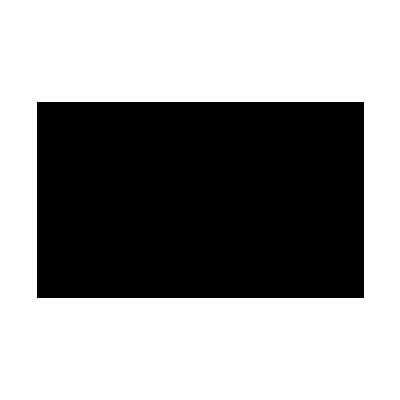

```mathematica
Table[conv[x1,y1],{x1,0,1,0.1},{y1,0,1,0.1}]
```

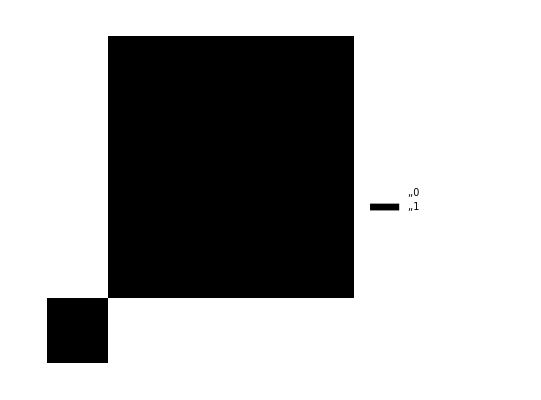

```mathematica
ArrayPlot[Table[fun[x,y,{1,2,0,0,0,0,0,0}],{x,0,1,0.25},{y,0,1,0.25}],PlotLegends->Automatic]
```

```mathematica
Union[Flatten[Table[Norm[(result/.{θ[1]->1,θ[2]->2,θ[3]->0,θ[4]->0,θ[5]->x1,θ[6]->x2,θ[7]->x3,θ[8]->x4}/.{x->1,y->1})[[2]]],{x1,0,Pi,Pi/4},{x2,0,Pi,Pi/4},{x3,0,Pi,Pi/4},{x4,0,Pi,Pi/4}]//N]]
```

{0.287797,0.287797}

```mathematica
Manipulate[
Table[ArrayPlot[data[[x1,x2,x3,x4,x5,x6,x7]],PlotLegends->Automatic],{x1,1,4},{x2,1,4}]//TableForm
,{x3,1,4,1},{x4,1,4,1},{x5,1,4,1},{x6,1,4,1},{x7,1,4,1}]
```

Part::partd: Part specification {«1»}⟦1,1,1,1,1,1,1⟧ is longer than depth of object.

ArrayPlot::mat: Argument {«1»}⟦1,1,1,1,1,1,1⟧ at position 1 is not a list of lists.

Part::partd: Part specification {«1»}⟦1,2,1,1,1,1,1⟧ is longer than depth of object.

ArrayPlot::mat: Argument {«1»}⟦1,2,1,1,1,1,1⟧ at position 1 is not a list of lists.

Part::partd: Part specification {«1»}⟦1,3,1,1,1,1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ArrayPlot::mat: Argument {«1»}⟦1,3,1,1,1,1,1⟧ at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

# Circuit 2

## Module

```mathematica
(*Gates*)
Rx[θ_]:={{Cos[θ/2],-I Sin[θ/2]},{-I Sin[θ/2],Cos[θ/2]}}
Ry[θ_]:={{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}}
Rz[θ_]:={{Exp[-I θ/2],0},{0,Exp[I θ/2]}}
cnot={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
(*Tensor calculation*)
TwoQubit[mat1_,mat2_]:=TensorProduct[mat1,mat2]//ArrayFlatten
FourQubit[{mat1_,mat2_,mat3_,mat4_}]:=TensorProduct[TwoQubit[mat1,mat2],TwoQubit[mat3,mat4]]//ArrayFlatten
```

```mathematica
(*Parameter condition*)
condition={θ[1]∈Reals,θ[1]≥0,θ[2]∈Reals,θ[2]≥0,θ[3]∈Reals,θ[3]≥0,θ[4]∈Reals,θ[4]≥0,θ[5]∈Reals,θ[5]≥0,θ[6]∈Reals,θ[6]≥0,θ[7]∈Reals,θ[7]≥0,θ[8]∈Reals,θ[8]≥0,1≥x≥0,1≥y≥0,x∈Reals,y∈Reals}
```

```mathematica
(*input state |0000>*)
input=Flatten[FourQubit[{0,1},{0,1},{0,1},{0,1}]];
(*Embedding Circuit*)
Embeding=Assuming[condition,FourQubit[Table[Rz[Pi/4],{i,1,4}]].FourQubit[Table[Ry[Pi/4],{i,1,4}]].FourQubit[Rx[x],Rx[y],Rx[x],Rx[y]]//Simplify];
(*Example Circuit 1*)
circuit1=Assuming[condition,TwoQubit[TwoQubit[cnot,{{1,0},{0,1}}],{{1,0},{0,1}}].TwoQubit[TwoQubit[{{1,0},{0,1}},cnot],{{1,0},{0,1}}].TwoQubit[TwoQubit[{{1,0},{0,1}},{{1,0},{0,1}}],cnot].FourQubit[Table[Rz[θ[i+4]],{i,1,4}]].FourQubit[Table[Rx[θ[i]],{i,1,4}]]];
```

```mathematica
(*result state*)
result=circuit1.Embeding.input;
(*Print First element*)
%[[1]]
```

-ⅈ ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) Cos[θ[1]/2] Cos[θ[2]/2] Cos[θ[3]/2] Cos[θ[4]/2] (Cos[x/2] Sin[π/8]+ⅈ Cos[π/8] Sin[x/2])^2 (Cos[y/2] Sin[π/8]+ⅈ Cos[π/8] Sin[y/2])^2-((-1)^(3/4) ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) Cos[θ[2]/2] Cos[θ[3]/2] Cos[θ[4]/2] (1+ⅈ Sin[x]) (Sin[1/8 (π-4 y)]+ⅈ Sin[1/8 (π+4 y)])^2 Sin[θ[1]/2])/(4 √2)-((-1)^(3/4) ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) Cos[θ[1]/2] Cos[θ[3]/2] Cos[θ[4]/2] (Sin[1/8 (π-4 x)]+ⅈ Sin[1/8 (π+4 x)])^2 (1+ⅈ Sin[y]) Sin[θ[2]/2])/(4 √2)+1/8 ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) Cos[θ[3]/2] Cos[θ[4]/2] (-ⅈ+Sin[x]) (-ⅈ+Sin[y]) Sin[θ[1]/2] Sin[θ[2]/2]-((-1)^(3/4) ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) Cos[θ[1]/2] Cos[θ[2]/2] Cos[θ[4]/2] (1+ⅈ Sin[x]) (Sin[1/8 (π-4 y)]+ⅈ Sin[1/8 (π+4 y)])^2 Sin[θ[3]/2])/(4 √2)+ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) Cos[θ[2]/2] Cos[θ[4]/2] (Cos[π/8] Cos[x/2]-ⅈ Sin[π/8] Sin[x/2])^2 (-ⅈ Cos[y/2] Sin[π/8]+Cos[π/8] Sin[y/2])^2 Sin[θ[1]/2] Sin[θ[3]/2]+1/8 ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) Cos[θ[1]/2] Cos[θ[4]/2] (-ⅈ+Sin[x]) (-ⅈ+Sin[y]) Sin[θ[2]/2] Sin[θ[3]/2]-((-1)^(1/4) ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) (Cos[1/8 (π-4 x)]+ⅈ Cos[1/8 (π+4 x)])^2 Cos[θ[4]/2] (1+ⅈ Sin[y]) Sin[θ[1]/2] Sin[θ[2]/2] Sin[θ[3]/2])/(4 √2)-((-1)^(3/4) ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) Cos[θ[1]/2] Cos[θ[2]/2] Cos[θ[3]/2] (Sin[1/8 (π-4 x)]+ⅈ Sin[1/8 (π+4 x)])^2 (1+ⅈ Sin[y]) Sin[θ[4]/2])/(4 √2)+1/8 ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) Cos[θ[2]/2] Cos[θ[3]/2] (-ⅈ+Sin[x]) (-ⅈ+Sin[y]) Sin[θ[1]/2] Sin[θ[4]/2]+ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) Cos[θ[1]/2] Cos[θ[3]/2] (Cos[x/2] Sin[π/8]+ⅈ Cos[π/8] Sin[x/2])^2 (ⅈ Cos[π/8] Cos[y/2]+Sin[π/8] Sin[y/2])^2 Sin[θ[2]/2] Sin[θ[4]/2]-((-1)^(1/4) ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) (Cos[1/8 (π-4 y)]+ⅈ Cos[1/8 (π+4 y)])^2 Cos[θ[3]/2] (1+ⅈ Sin[x]) Sin[θ[1]/2] Sin[θ[2]/2] Sin[θ[4]/2])/(4 √2)+1/8 ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) Cos[θ[1]/2] Cos[θ[2]/2] (-ⅈ+Sin[x]) (-ⅈ+Sin[y]) Sin[θ[3]/2] Sin[θ[4]/2]-((-1)^(1/4) ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) (Cos[1/8 (π-4 x)]+ⅈ Cos[1/8 (π+4 x)])^2 Cos[θ[2]/2] (1+ⅈ Sin[y]) Sin[θ[1]/2] Sin[θ[3]/2] Sin[θ[4]/2])/(4 √2)-((-1)^(1/4) ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) (Cos[1/8 (π-4 y)]+ⅈ Cos[1/8 (π+4 y)])^2 Cos[θ[1]/2] (1+ⅈ Sin[x]) Sin[θ[2]/2] Sin[θ[3]/2] Sin[θ[4]/2])/(4 √2)+ⅈ ⅇ^(-1/2 ⅈ θ[5]-1/2 ⅈ θ[6]-1/2 ⅈ θ[7]-1/2 ⅈ θ[8]) (Cos[π/8] Cos[x/2]-ⅈ Sin[π/8] Sin[x/2])^2 (Cos[π/8] Cos[y/2]-ⅈ Sin[π/8] Sin[y/2])^2 Sin[θ[1]/2] Sin[θ[2]/2] Sin[θ[3]/2] Sin[θ[4]/2]

```mathematica
result
```

## Test

```mathematica
(*Test Norm is equal to 1*)
Norm[result/.Table[θ[i]->1,{i,1,8}]/.{x->1,y->1}//N]
```

1.

```mathematica
(*Probability amplitute for each base*)
ProbAmp1=Table[Norm[(result[[j]]/.Table[θ[i]->0,{i,1,8}]/.{x->1,y->1})//N],{j,1,16}];
(*Sum of Prob square eqaul to 1*)
Total[ProbAmp1^2]
```

1.

```mathematica
fun[x1_,y1_,param1_]:=Module[{param,data,loc,conv,max,ProbAmp},
param=Table[θ[i]->param1[[i]],{i,1,8}];
data={x->x1,y->y1};
ProbAmp=Table[Norm[(result[[j]]/.param/.data)],{j,1,16}];
max=Max[ProbAmp];
loc=Position[ProbAmp,max][[1,1]];
conv=If[MemberQ[{1,2,3,4,13,14,15,16},loc],0,1];
conv
]
```

```mathematica
Clear[dataStorage]
dataStorage[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_]:=dataStorage[x1,x2,x3,x4,x5,x6,x7,x8]=Table[fun[x,y,{x1,x2,x3,x4,x5,x6,x7,x8}],{x,0,1,0.25},{y,0,1,0.25}]
```

```mathematica
result[[1]]/.{x->0,y->0}//TrigToExp//Simplify
```

1/64 ⅇ^(-1/2 ⅈ (θ[1]+θ[2]+θ[3]+θ[4]+θ[5]+θ[6]+θ[7]+θ[8])) (-1+(-ⅈ+√2) ⅇ^(ⅈ θ[1])+(-ⅈ+√2) ⅇ^(ⅈ θ[2])+(-1+2 ⅈ √2) ⅇ^(ⅈ (θ[1]+θ[2]))+(-ⅈ+√2) ⅇ^(ⅈ θ[3])+(-1+2 ⅈ √2) ⅇ^(ⅈ (θ[1]+θ[3]))+(-1+2 ⅈ √2) ⅇ^(ⅈ (θ[2]+θ[3]))-(5 ⅈ+√2) ⅇ^(ⅈ (θ[1]+θ[2]+θ[3]))+(-ⅈ+√2) ⅇ^(ⅈ θ[4])+(-1+2 ⅈ √2) ⅇ^(ⅈ (θ[1]+θ[4]))+(-1+2 ⅈ √2) ⅇ^(ⅈ (θ[2]+θ[4]))-(5 ⅈ+√2) ⅇ^(ⅈ (θ[1]+θ[2]+θ[4]))+(-1+2 ⅈ √2) ⅇ^(ⅈ (θ[3]+θ[4]))-(5 ⅈ+√2) ⅇ^(ⅈ (θ[1]+θ[3]+θ[4]))-(5 ⅈ+√2) ⅇ^(ⅈ (θ[2]+θ[3]+θ[4]))+(7+4 ⅈ √2) ⅇ^(ⅈ (θ[1]+θ[2]+θ[3]+θ[4])))

```mathematica
elem1=result[[1]]/.{x->0,y->0}//TrigToExp//Simplify
```

1/64 ⅇ^(-1/2 ⅈ (θ[1]+θ[2]+θ[3]+θ[4]+θ[5]+θ[6]+θ[7]+θ[8])) (-1+(-ⅈ+√2) ⅇ^(ⅈ θ[1])+(-ⅈ+√2) ⅇ^(ⅈ θ[2])+(-1+2 ⅈ √2) ⅇ^(ⅈ (θ[1]+θ[2]))+(-ⅈ+√2) ⅇ^(ⅈ θ[3])+(-1+2 ⅈ √2) ⅇ^(ⅈ (θ[1]+θ[3]))+(-1+2 ⅈ √2) ⅇ^(ⅈ (θ[2]+θ[3]))-(5 ⅈ+√2) ⅇ^(ⅈ (θ[1]+θ[2]+θ[3]))+(-ⅈ+√2) ⅇ^(ⅈ θ[4])+(-1+2 ⅈ √2) ⅇ^(ⅈ (θ[1]+θ[4]))+(-1+2 ⅈ √2) ⅇ^(ⅈ (θ[2]+θ[4]))-(5 ⅈ+√2) ⅇ^(ⅈ (θ[1]+θ[2]+θ[4]))+(-1+2 ⅈ √2) ⅇ^(ⅈ (θ[3]+θ[4]))-(5 ⅈ+√2) ⅇ^(ⅈ (θ[1]+θ[3]+θ[4]))-(5 ⅈ+√2) ⅇ^(ⅈ (θ[2]+θ[3]+θ[4]))+(7+4 ⅈ √2) ⅇ^(ⅈ (θ[1]+θ[2]+θ[3]+θ[4])))

```mathematica
elem1/.{θ[1]->0,θ[2]->0}//Simplify
```

(1/32+ⅈ/32) ⅇ^(-1/2 ⅈ (θ[3]+θ[4]+θ[5]+θ[6]+θ[7]+θ[8])) (-1+√2+((-2-ⅈ)+(1+ⅈ) √2) ⅇ^(ⅈ θ[3])+((-2-ⅈ)+(1+ⅈ) √2) ⅇ^(ⅈ θ[4])+((-1-4 ⅈ)+(1+2 ⅈ) √2) ⅇ^(ⅈ (θ[3]+θ[4])))

```mathematica
param1={0.5,0.5,1,1,0,0,0,0};
param=Table[θ[i]->param1[[i]],{i,1,8}];
data1={x->0.6,y->0.6};
ProbAmp=Table[Norm[(result[[j]]/.param/.data1)],{j,1,16}]
max=Max[ProbAmp]
Position[ProbAmp,max]
```

{0.0810462,0.113754,0.159662,0.113754,0.28357,0.202035,0.143944,0.202035,0.503639,0.358827,0.255653,0.358827,0.143944,0.202035,0.28357,0.202035}

0.503639

{{9}}

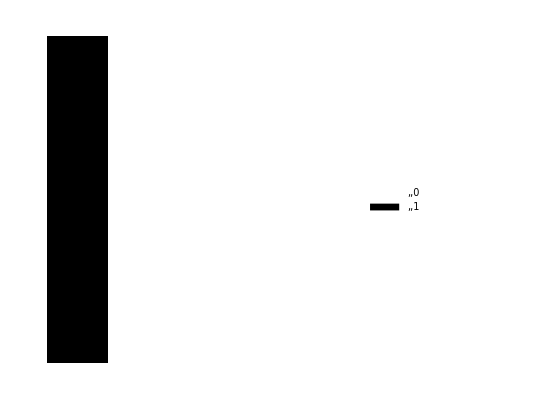

```mathematica
ArrayPlot[Table[fun[x,y,{1,2,0,0,0,0,0,0}],{x,0,1,0.25},{y,0,1,0.25}],PlotLegends->Automatic]
```

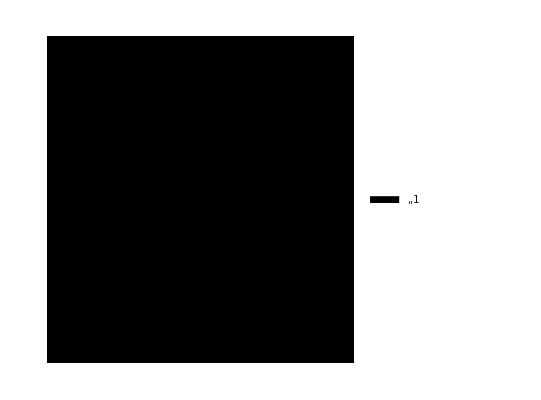

```mathematica
ArrayPlot[Table[fun[x,y,{0,0,0,0,0,0,0,0}],{x,0,1,0.25},{y,0,1,0.25}],PlotLegends->Automatic]
```

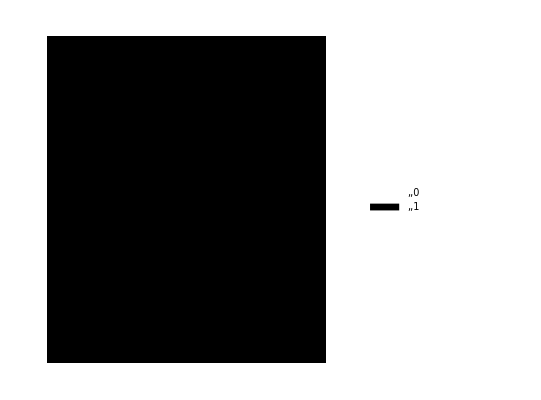

```mathematica
ArrayPlot[Table[fun[x,y,{1,1,Pi/2,0,0,1,0,1}],{x,0,1,0.1},{y,0,1,0.1}],PlotLegends->Automatic]
```

```mathematica
ArrayPlot[Table[fun[x,y,{1,1,3/2Pi,3/2Pi,0,0,0,1}],{x,0,1,0.1},{y,0,1,0.1}],PlotLegends->Automatic]
```

-Graphics-